Phase plot of the rescaled equations

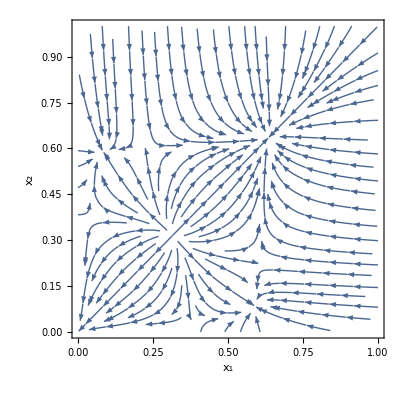

```mathematica
Subscript[ϵ, 2]=0.5;
Subscript[ϵ, 3]=0.95;
Subscript[β, 2]=0.2;
Subscript[β, 3]=4;
StreamPlot[{-Subscript[x, 1]+Subscript[β, 2]/2(1-Subscript[x, 1])((Subscript[x, 1]+Subscript[x, 2])+Subscript[ϵ, 2](Subscript[x, 1]-Subscript[x, 2]))+Subscript[β, 3]/4(1-Subscript[x, 1])((Subscript[x, 1]+Subscript[x, 2])^2+Subscript[ϵ, 3](3 Subscript[x, 1]^2-2 Subscript[x, 1] Subscript[x, 2]-Subscript[x, 2]^2)),- Subscript[x, 2]+Subscript[β, 2]/2(1-Subscript[x, 2])((Subscript[x, 1]+Subscript[x, 2])+Subscript[ϵ, 2](Subscript[x, 2]-Subscript[x, 1]))+Subscript[β, 3]/4(1-Subscript[x, 2])((Subscript[x, 1]+Subscript[x, 2])^2+Subscript[ϵ, 3](3 Subscript[x, 2]^2-2 Subscript[x, 1] Subscript[x, 2]-Subscript[x, 1]^2))},{Subscript[x, 1],0,1},{Subscript[x, 2],0,1},Axes->True,FrameLabel->{"x_1","x_2"},LabelStyle->Directive[Black,Bold,16], PlotRange->{{0,1},{0,1}},StreamColorFunction->None]
```

Imbalanced case

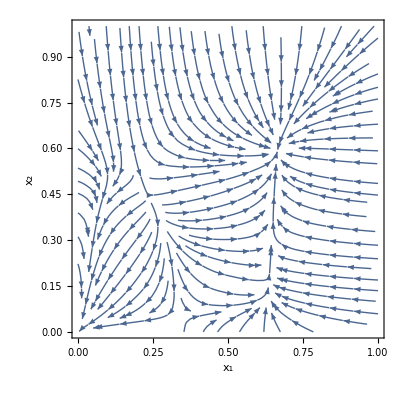

```mathematica
k=20;
q=20;
Subscript[ϵ, 2]=0.18;
Subscript[ϵ, 3]=0.95;
ρ=0.515;
γ=1;
Subscript[β, 2]=0.2/k;
Subscript[β, 3]=4/q;
Subscript[r, 2]=(1-ρ^2-(1-ρ)^2)/(ρ^2+(1-ρ)^2);
Subscript[r, 3]=(1-ρ^3-(1-ρ)^3)/(ρ^3+(1-ρ)^3);
StreamPlot[{-γ Subscript[x, 1]+Subscript[β, 2] k(1-Subscript[x, 1])(ρ(1+Subscript[r, 2] Subscript[ϵ, 2])Subscript[x, 1]+(1-ρ)(1-Subscript[ϵ, 2])Subscript[x, 2])+Subscript[β, 3] q(1-Subscript[x, 1])(ρ^2(1+Subscript[r, 3] Subscript[ϵ, 3])Subscript[x, 1]^2+2(1-ρ)ρ(1-Subscript[ϵ, 3])Subscript[x, 1] Subscript[x, 2]+(1-ρ)^2(1-Subscript[ϵ, 3])Subscript[x, 2]^2),-γ Subscript[x, 2]+Subscript[β, 2] k(1-Subscript[x, 2])((1-ρ)(1+Subscript[r, 2] Subscript[ϵ, 2])Subscript[x, 2]+ρ(1-Subscript[ϵ, 2])Subscript[x, 1])+Subscript[β, 3] q(1-Subscript[x, 2])((1-ρ)^2(1+Subscript[r, 3] Subscript[ϵ, 3])Subscript[x, 2]^2+2(1-ρ)ρ(1-Subscript[ϵ, 3])Subscript[x, 2] Subscript[x, 1]+ρ^2(1-Subscript[ϵ, 3])Subscript[x, 1]^2)},{Subscript[x, 1],0,1},{Subscript[x, 2],0,1},Axes->True,FrameLabel->{"x_1","x_2"},LabelStyle->Directive[Black,Bold,24], PlotRange->{{0,1},{0,1}},StreamColorFunction->None]
```

```mathematica
Manipulate[Subscript[r, 2]=(1-ρ^2-(1-ρ)^2)/(ρ^2+(1-ρ)^2);
Subscript[r, 3]=(1-ρ^3-(1-ρ)^3)/(ρ^3+(1-ρ)^3);
StreamPlot[{-γ Subscript[x, 1]+Subscript[β, 2] k(1-Subscript[x, 1])(ρ(1+Subscript[r, 2] Subscript[ϵ, 2])Subscript[x, 1]+(1-ρ)(1-Subscript[ϵ, 2])Subscript[x, 2])+Subscript[β, 3] q(1-Subscript[x, 1])(ρ^2(1+Subscript[r, 3] Subscript[ϵ, 3])Subscript[x, 1]^2+2(1-ρ)ρ(1-Subscript[ϵ, 3])Subscript[x, 1] Subscript[x, 2]+(1-ρ)^2(1-Subscript[ϵ, 3])Subscript[x, 2]^2),-γ Subscript[x, 2]+Subscript[β, 2] k(1-Subscript[x, 2])((1-ρ)(1+Subscript[r, 2] Subscript[ϵ, 2])Subscript[x, 2]+ρ(1-Subscript[ϵ, 2])Subscript[x, 1])+Subscript[β, 3] q(1-Subscript[x, 2])((1-ρ)^2(1+Subscript[r, 3] Subscript[ϵ, 3])Subscript[x, 2]^2+2(1-ρ)ρ(1-Subscript[ϵ, 3])Subscript[x, 2] Subscript[x, 1]+ρ^2(1-Subscript[ϵ, 3])Subscript[x, 1]^2)},{Subscript[x, 1],0,1},{Subscript[x, 2],0,1},Axes->True,FrameLabel->{"x_1","x_2"},LabelStyle->Directive[Black,Bold,16],StreamColorFunction->None, PlotRange->{{0,1},{0,1}}],{ρ,0,1,0.01}]
```